# Wolfram Mathematica Tutorial for Math Students

## Notebook Documents

You can use Wolfram notebooks, which mix text, graphics, interfaces, etc. with computations. 

Notebooks are organized in cells, indicated by brackets on the right. 
Double-click a cell bracket to open or close a group of cells. 
Click between cells to get a horizontal insertion bar to create a new cell.
Copy, paste, delete, etc. any collection of cells.
Select any collection of cells and press SHIFT+ENTER to evaluate inputs.
You can make title, section or text cells in a notebook: (Alt + 1, Alt + 4, Alt +7, respectively)
You can convert your notebook to a slide show
Like everything else in the Wolfram Language, documents are symbolic expressions that can be altered programmatically.

## Entering Input

press SHIFT+ENTER to compute:

```mathematica
2+2
```

4

In[n] and Out[n] label successive inputs and outputs. The % symbol refers to the most recent output:

```mathematica
1+2+3
```

6

```mathematica
%+4
```

10

The Wolfram Language has nearly 6,000 built-in functions, covering many areas of mathematics. Arguments to built-in functions are separated by commas and enclosed in square brackets:

```mathematica
GCD[12,15]
```

3

If you don’t know what function to use, type = at the beginning of a line for natural-language input:

plot a sine curve

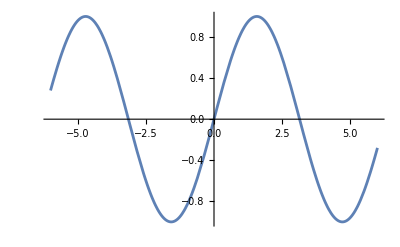

```mathematica
Plot[Evaluate[Sin[x]], {x, -6., 6.}]
```

Lists represent collections of items and are indicated by { ... }.  Lists are ordered. They can contain numbers, variables, computations or even other lists.
Many operations are applied elementwise.  Starting at 1, parts of lists can be extracted using [[ ... ]]:

```mathematica
{1,2,3}
{x,y,z}
```

{1,2,3}

{x,y,z}

```mathematica
{1,2,3}+2
```

{3,4,5}

```mathematica
{a,b,c,d}[[3]]
```

c

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

## Fractions & Decimals

In the Wolfram Language, exact input (like fractions) will provide exact output: (Use CTRL+ / to enter fractions.)

```mathematica
1/4+1/3
```

7/12

Put fractions over their lowest common denominator with Together:

```mathematica
Together[1/a+1/b]
```

(a+b)/(a b)

Any input containing decimals gives approximate output:

```mathematica
.25+1/3
```

0.583333

Use N to get a numerical approximation of a result and specify the accuracy to which your answer is displayed

```mathematica
N[1/4+1/7, 10]
```

0.3928571429

```mathematica
ScientificForm[0.00123]
```

1.23×10^-3

## Variables & Functions

A space between two variables or numbers indicates multiplication. Use /. and → to make substitutions in an expression:

```mathematica
a b+5 x x
1+2 x/. x->2
```

a b+5 x^2

5

Clear the assignment, and x remains unevaluated:

```mathematica
Clear[x]
1+2 x
```

1+2 x

Define your own functions with the construction f[x_]:=

x_ means that x is a pattern that can have any value substituted for it.
:= means that any argument passed to f is substituted into the right-hand side upon evaluation:

```mathematica
f[x_]:=1+2 x
f[2]
```

5

## Algebra

You can factor or expand algebraic expressions:

```mathematica
Factor[x^2+2 x+1]
```

(1+x)^2

The Wolfram Language uses == (two equal signs) to test equality:

```mathematica
2==2
```

True

Combine algebraic expressions with == to represent an equation:

```mathematica
1+z==15
```

1+z==15

Commands like Solve find exact solutions to equations:

```mathematica
Solve[x^2+5 x-6==0,x]
```

{{x→-6},{x→1}}

For approximate results, use NSolve:

```mathematica
NSolve[7 x^2+3 x-5==0,x]
```

{{x→-1.08618},{x→0.657611}}

Pass in a system of equations as a list:

```mathematica
Solve[{x^2+5==y,7 x-5==y},{x,y}]
```

{{x→2,y→9},{x→5,y→30}}

Find the roots of an equation: (|| is the symbol for Or.)

```mathematica
Roots[x^2+3 x-4==0,x]
```

x==-4||x==1

If a polynomial is not easily factorable, approximate results may be more useful:

```mathematica
NRoots[360+234 x-1051 x^2+11 x^3+304 x^4-20 x^5==0,x]
```

x==-1.79025||x==-0.498678||x==0.797819||x==1.68398||x==15.0071

The Reduce command reduces a set of inequalities into a simple form:

```mathematica
Reduce[{0<x<2,1<=x<=4},x]
```

1≤x<2

```mathematica
Reduce[(x-1) (x-2) (x-3) (x-4)>0,x]
```

x<1||2<x<3||x>4

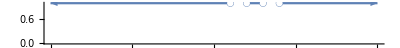

```mathematica
NumberLinePlot[x<1||2<x<3||x>4,{x,-10,10}]
```

Many equations and formulas are available through natural-language input:

WolframAlphaQueryResults

x^2-2 x+1==0
a x^2+b x+c==0 | 
x | indeterminate variable
a | quadratic coefficient
b | linear coefficient
c | constant coefficient
(x==(-b±√(b^2-4 a c))/(2 a))

## Plots in 2D

Note that The interval notation of {x,min,max} defines the domain. (&& is the symbol for And.)

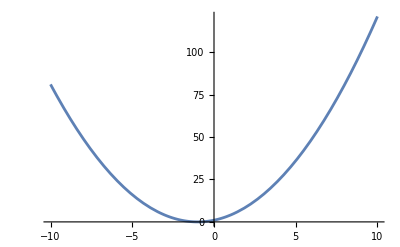

```mathematica
Plot[x^2+2 x+1,{x,-10,10}]
```

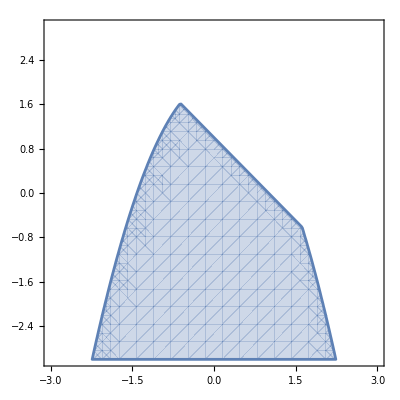

```mathematica
RegionPlot[Reduce[{x^2+y<2&&x+y<1}],{x,-3,3},{y,-3,3}]
```

There are lots of useful options to customize visualizations, like adding legends Or filling a plot to visualize the area under a curve:

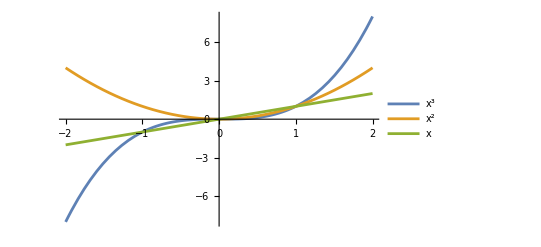

```mathematica
Plot[{x^3,x^2,x},{x,-2,2},PlotLegends->"Expressions"]
```

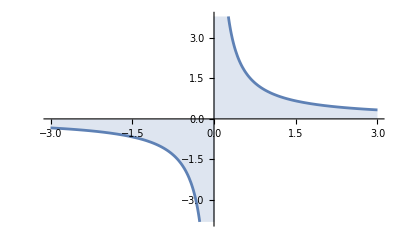

```mathematica
Plot[1/x,{x,-3,3},Filling->Axis]
```

Combine different plot types with Show:

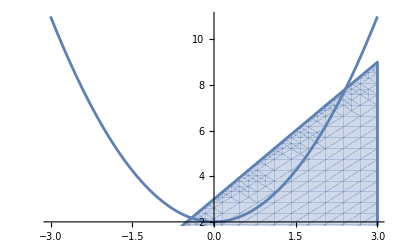

```mathematica
Show[{Plot[x^2+2,{x,-3,3}],RegionPlot[2 x>y-3,{x,-3,3},{y,0,9}]}]
```

## Trigonometry

For basic trig functions, use standard abbreviations (with the first letter capitalized) , Add “Arc” for the inverses:

```mathematica
Sin[x]/Cos[x]==Tan[x]
```

True

```mathematica
ArcTan[1]
```

π/4

Use Pi when working with radian expressions (Type ESCpiESC for the π character.) Or type ESCdegESC for the built-in Degree symbol:

```mathematica
Sin[π/2]
```

1

```mathematica
Sin[90 °]
```

1

Automatically expand (or reduce) trig expressions using identities:

```mathematica
TrigExpand[Sin[2 x]]
```

2 Cos[x] Sin[x]

```mathematica
TrigFactor[Cos[x]^2-Sin[x]^2]
```

2 Sin[π/4-x] Sin[π/4+x]

Functions like Solve work as well:

```mathematica
Solve[Cos[x]^2+Sin[x]^2==x]
```

{{x→1}}

```mathematica
Solve[{Tan[x]==1,0<x<2 Pi}]
```

{{x→π/4},{x→(5 π)/4}}

## Exponentials & Logarithms

The Wolfram Language represents the exponential constant as E. Log gives the natural logarithm of an expression:

```mathematica
Log[E^2]
```

2

```mathematica
Log[2,64]
```

6

Make plots on a logarithmic scale:

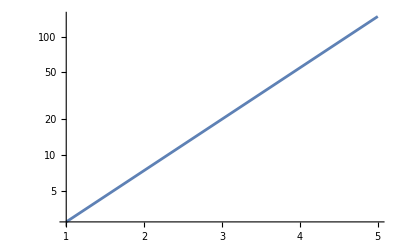

```mathematica
LogPlot[E^x,{x,1,5}]
```

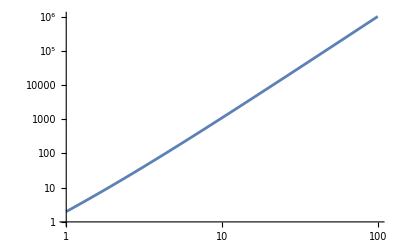

```mathematica
LogLogPlot[x^2+x^3,{x,1,100}]
```

## Limits

Calculate the limiting value of an expression: (Type -> for the → symbol.) (Type ESC inf ESC for the ∞ symbol.))

```mathematica
Limit[(x^3-1)/(x-1),x->1]
```

3

```mathematica
Limit[(2 x^3-1)/(5 x^3+x-1),x->∞]
```

2/5

```mathematica
Limit[1/x,x->0,Direction->1]
```

-∞

```mathematica
Limit[1/x,x->0,Direction->-1]
```

∞

Use HoldForm to leave the expression unevaluated: (TraditionalForm uses classic mathematical typesetting.)

```mathematica
TraditionalForm[HoldForm[Limit[1/x,x->Infinity]]]
```

1/xx∞

## Derivatives

Calculate derivatives with the D command Or use prime notation:

```mathematica
D[x^6,x]
Sin'[x]

f[x_]:=x^2+2 x+1;
f'[x]
```

6 x^5

Cos[x]

2+2 x

You can Pass derivatives directly into a plot:

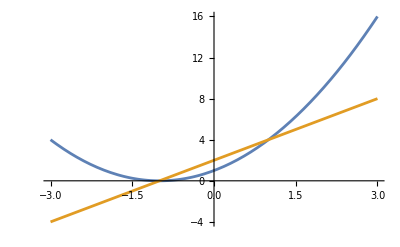

```mathematica
Plot[{f[x],f'[x]},{x,-3,3}]
```

You can also take multiple derivatives:

```mathematica
D[x^6,{x,3}]
Sin''[x]
```

120 x^3

-Sin[x]

calculus formulas can be accessed via natural-language input:

WolframAlphaQueryParseResults

{d/dx(f(x) g(x)) == f(x) g'(x) + g(x) f'(x)}

## Integrals

Compute integrals with Integrate Or type ESC intt ESC for a fillable mathematical expression:

```mathematica
Integrate[8 x^4,x]
```

(8 x^5)/5

```mathematica
∫8 x^4 ⅆx
```

(8 x^5)/5

For definite integrals, type ESCdinttESC and specify upper and lower limits:

```mathematica
∫_0^π Sin[x]ⅆx
```

2

Use NIntegrate for a numeric approximation:

```mathematica
NIntegrate[x^3 Sin[x]+2 Log[3 x]^2,{x,0,Pi}]
```

28.1531

## Sequences, Sums & Series

In the Wolfram Language, integer sequences are represented by lists.

Use Table to define a simple sequence (Some well-known sequences are built in):

```mathematica
Table[x^2,{x,1,7}]
```

{1,4,9,16,25,36,49}

```mathematica
Table[Fibonacci[x],{x,1,7}]
```

{1,1,2,3,5,8,13}

Define a recursive sequence using RecurrenceTable: (Note the use of {x,min,max} notation.)

```mathematica
RecurrenceTable[{a[x]==2 a[x-1],a[1]==1},a,{x,1,8}]
```

{1,2,4,8,16,32,64,128}

Compute the Total of the sequence:

```mathematica
Total[%]
```

255

Compute the Sum of a sequence from its generating function:

```mathematica
Sum[i (i+1),{i,1,10}]
```

440

Use ESC sumt ESC for a fillable typeset form:

```mathematica
∑_(i=1)^10 i(i+1)
```

440

You can do indefinite and multiple sums too:

```mathematica
∑_(i=1)^n ∑_(j=1)^n i j
```

1/4 n^2 (1+n)^2

Calculate a generating function for a sequence:

```mathematica
FindSequenceFunction[{2,4,6,8},n]
```

2 n

Generate power series approximations to virtually any combination of built-in functions:

```mathematica
Series[Exp[x^2],{x,0,8}]
```

1+x^2+x^4/2+x^6/6+x^8/24+O[x]^9

O[x]9 represents higher-order terms that have been omitted; use Normal to truncate this term:

```mathematica
Normal[%]
```

1+x^2+x^4/2+x^6/6+x^8/24

Given an unknown or undefined function, Series returns a power series in terms of derivatives:

```mathematica
Clear[f]
Series[2 f[x]-3,{x,0,3}]
```

(-3+2 f[0])+2 f'[0] x+f''[0] x^2+1/3 f^(3)[0] x^3+O[x]^4

## Plots in 3D

## Multivariate Calculus

D works for partial derivatives—just specify which variable(s) to differentiate:

```mathematica
D[x^3 z+2 y^2 x+y z^3,y,z]
```

3 z^2

Or use the ∂ symbol: Type ESCpdESC for ∂ and CTRL+- for subscript

```mathematica
D[(x^2 - 2x y + x y z), x]
```

2 x-2 y+y z

```mathematica
D[(x^2-2x y+x y z), x,y]
```

-2+z

Multiple integrals use the same notation as single integrals: (Type ESCintESC for ∫ and ESCddESC for ⅆ.)

```mathematica
∫∫∫(x^2 + y^2 +z^2)ⅆy ⅆx ⅆz
```

1/3 x^3 y z+1/3 x y^3 z+1/3 x y z^3

```mathematica
Factor[%]
```

1/3 x y z (x^2+y^2+z^2)

Symbolic results can often be quite complicated:

```mathematica
∫_-1^1 ∫_-2^x (x Sin[y^2]+y Cos[x^2])ⅆyⅆx
```

1/4 (2 Cos[1]+√(2 π) (-9 FresnelC[√(2/π)]+FresnelS[√(2/π)])+2 Sin[1])

When this happens, you can always get an approximate output by using the N command:

```mathematica
N[%,5]
```

-3.2243

## Vector Analysis & Visualization

n-dimensional vectors are represented by lists of length n.

```mathematica
{1,2,3}.{a,b,c}
```

a+2 b+3 c

Type ESC cross ESC for the cross product symbol:

```mathematica
{1,2,c}×{a,b,c}
```

{2 c-b c,-c+a c,-2 a+b}

```mathematica
Norm[{1,1,1}]
```

√3

```mathematica
Projection[{8,6,7},{1,0,0}]
```

{8,0,0}

Angle between two vectors

```mathematica
VectorAngle[{1,0},{0,1}]
```

π/2

Calculate the gradient of a vector: (For the ∇ symbol, use ESCgradESC.)

```mathematica
∇_{x,y} {x^2+y,x+y^2}
```

{{2 x,1},{1,2 y}}

```mathematica
Div[{f[x,y,z],g[x,y,z],h[x,y,z]},{x,y,z}]
```

h^(0,0,1)[x,y,z]+g^(0,1,0)[x,y,z]+f^(1,0,0)[x,y,z]

The Wolfram Language has 2D and 3D functions suitable for visualizing vector fields:

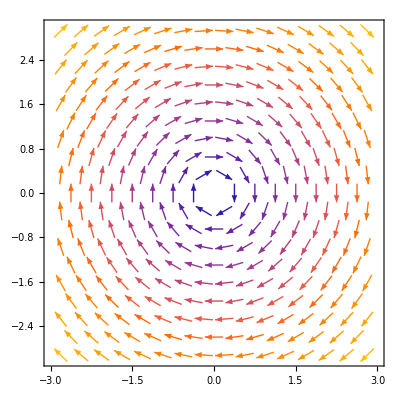

```mathematica
VectorPlot[{y,-x},{x,-3,3},{y,-3,3}]
```

```mathematica
VectorPlot3D[{y,-x,z},{x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-

Plot a vector field over a slice surface:

```mathematica
SliceVectorPlot3D[{y,-x,z},"CenterPlanes",{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

## Differential Equations

The Wolfram Language can find solutions to ordinary, partial and delay differential equations (ODEs, PDEs and DDEs). DSolveValue takes a differential equation and returns the general solution: (C[1] stands for a constant of integration.)

```mathematica
sol=DSolveValue[y'[x]+y[x]==x,y[x],x]
```

-1+x+ⅇ^-x C[1]

Use /. to replace the constant:

```mathematica
sol/. C[1]->1
```

-1+ⅇ^-x+x

Or add conditions for a specific solution:

```mathematica
DSolveValue[{y'[x]+y[x]==x,y[0]==-1},y[x],x]
```

-1+x

NDSolveValue finds numerical solutions. You can plot this InterpolatingFunction directly:

```mathematica
NDSolveValue[{y'[x]==Cos[x^2],y[0]==0},y[x],{x,-5,5}]
```

InterpolatingFunction[…][x]

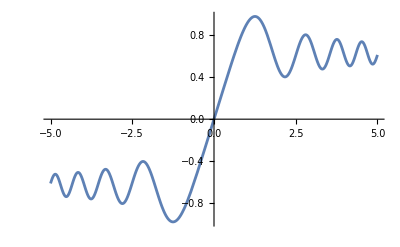

```mathematica
Plot[%,{x,-5,5}]
```

To solve systems of differential equations, include all equations and conditions in a list: (Note that the line breaks have no effect.)

```mathematica
{xsol,ysol}=NDSolveValue[{x'[t]==-y[t]-x[t]^2,y'[t]==2 x[t]-y[t]^3,x[0]==y[0]==1},{x,y},{t,20}]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

Visualize the solution as a parametric plot:

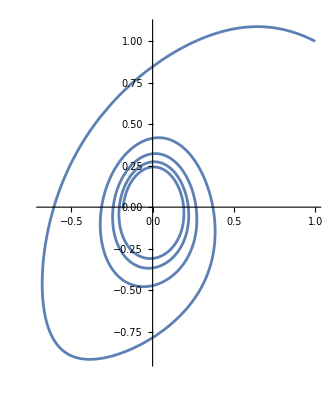

```mathematica
ParametricPlot[{xsol[t],ysol[t]},{t,0,20}]
```

## Complex Analysis

The imaginary unit is represented as I. Most operations automatically handle complex numbers:

```mathematica
I^2
```

-1

```mathematica
(1+I) (2-3 I)
```

5-ⅈ

We can Expand complex expressions and Convert expressions between exponential and trig forms:

```mathematica
ComplexExpand[Sin[x+I y]]
```

Cosh[y] Sin[x]+ⅈ Cos[x] Sinh[y]

```mathematica
ExpToTrig[E^(I x)]
```

Cos[x]+ⅈ Sin[x]

```mathematica
TrigToExp[%]
```

ⅇ^(ⅈ x)

Type ESCcoESC for the Conjugate symbol:

```mathematica
(3+2 I)*
```

3-2 ⅈ

Extract the real and imaginary parts of an expression, Or find the absolute value and argument:

```mathematica
ReIm[3+2 I]
```

{3,2}

```mathematica
AbsArg[(1+I)]
```

{√2,π/4}

## Matrices & Linear Algebra

The Wolfram Language represents matrices as lists of lists. Enter a table using CTRL+ ENTER for rows and CTRL+ , for columns:

```mathematica
{{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
{{a, b}, {c, d}}
```

{{a,b},{c,d}}

MatrixForm displays output as a matrix:

```mathematica
MatrixForm[{{a,b},{c,d}}]
```

(a | b
c | d)

You can construct a matrix with iterative functions:

```mathematica
Table[x+y,{x,1,3},{y,0,2}]
```

{{1,2,3},{2,3,4},{3,4,5}}

```mathematica
Import["data.csv"]
```

Import::nffil: File data.csv not found during Import.

$Failed

Standard matrix operations work elementwise:

```mathematica
{1,2,3} {a,b,c}
```

{a,2 b,3 c}

Compute the dot product of two matrices:

```mathematica
{{1,2},{3,4}}.{{a,b},{c,d}}
```

{{a+2 c,b+2 d},{3 a+4 c,3 b+4 d}}

Find the determinant and get the inverse:

```mathematica
Det[{{a,b},{c,d}}]
```

-b c+a d

```mathematica
Inverse[{{1,1},{0,1}}]
```

{{1,-1},{0,1}}

Use LinearSolve to solve a linear system:

```mathematica
LinearSolve[{{1,1},{0,1}},{x,y}]
```

{x-y,y}

## Probability

The Wolfram Language contains a wide range of functions for probability, as well as hundreds of symbolic distributions. 
Calculate factorials using mathematical notation, For combinations, use Binomial,

```mathematica
5!
```

120

```mathematica
Binomial[4,3]
```

4

Compute probabilities for a binomial distribution: (Type ESCdistESC for the \[Distributed] symbol.

```mathematica
Probability[x==1,x\[Distributed]BinomialDistribution[1,1/2]]
```

1/2

Calculate the expectation of a polynomial expression:

```mathematica
Expectation[2 x+3,x\[Distributed]NormalDistribution[]]
```

3

Get the PDF for a normal distribution in symbolic form:

```mathematica
PDF[NormalDistribution[0,1],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

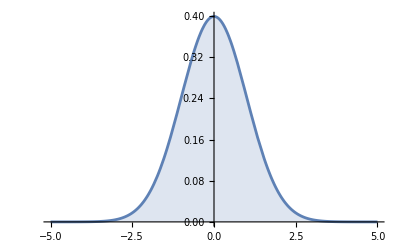

```mathematica
Plot[%,{x,-5,5},Filling->Axis]
```

Free-form input can be used to calculate the probability of real-world events:

WolframAlphaQueryResults

First::nofirst: {} has zero length and no first element.

| probability | chance
at least 2 the same | 0.3469 | ≈ 1 in 3
at least 3 the same | 0.005929 | ≈ 1 in 169
(assuming people chosen independently and all 365 possible birthdays are equally likely)

## Statistics

In the Wolfram Language, statistical functions accept either lists or symbolic distributions as an argument.

```mathematica
Mean[{1,2,4,5}]
```

3

```mathematica
Correlation[{1,3,5},{6,4,2}]
```

-1

```mathematica
StandardDeviation[PoissonDistribution[2]]
```

√2

```mathematica
Moment[{x,y,z},2]
```

1/3 (x^2+y^2+z^2)

Get the moment-generating function for a distribution: (Type ESC m ESC for μ and ESC s ESC for σ.)

```mathematica
MomentGeneratingFunction[NormalDistribution[μ,σ],t]
```

ⅇ^(t μ+(t^2 σ^2)/2)

Generate statistical data with RandomVariate: (Use //Short to get a short summary of output.)

```mathematica
RandomVariate[NormalDistribution[0,1],{500,2}]//Short
```

{{0.591198,1.03368},{0.439111,0.5867},«497»,{0.176943,0.489586}}

```mathematica
Histogram3D[%]
```

-Graphics3D-

## Data Plots & Best-Fit Curves

Use ListPlot to visualize data as a scatterplot. Or display information as a chart:

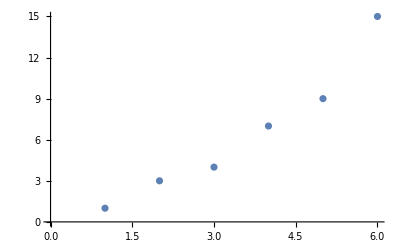

```mathematica
ListPlot[{1,3,4,7,9,15}]
```

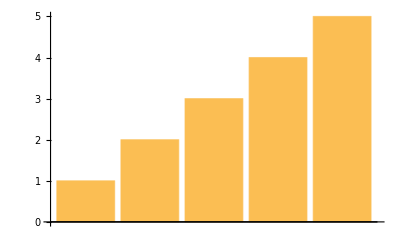

```mathematica
BarChart[{1,2,3,4,5}]
```

There are also specialized functions for time series, financial data and much more. Multiple datasets are automatically colored differently:

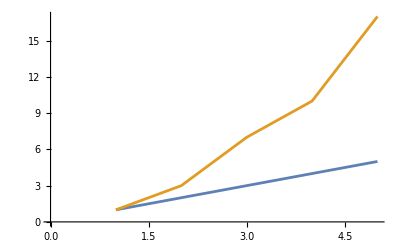

```mathematica
ListLinePlot[{{1,2,3,4,5},{1,3,7,10,17}}]
```

You can change the style and appearance of plots using options like PlotTheme. Find a curve of best fit with the Fit command: ({1,x,x2} means a quadratic fit over x.)

```mathematica
Fit[{2,3,5,7,11,13},{1,x,x^2},x]
```

0.9+0.689286 x+0.232143 x^2

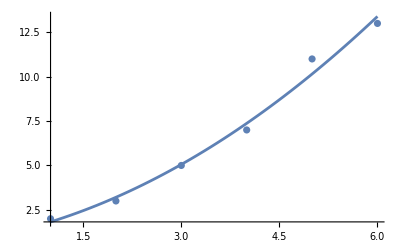

```mathematica
Show[{Plot[%,{x,1,6}],ListPlot[{2,3,5,7,11,13}]}]
```

## Interactive Models

The Manipulate command lets you interactively explore what happens when you vary parameters in real time:

```mathematica
Manipulate[Plot[Sin[f x],{x,-3,3},Filling->Axis],{f,1,5}]
```

A single Manipulate command can have multiple controllers, and the Wolfram Language automatically chooses the best layout of those controllers for you:

```mathematica
Manipulate[Plot[Sin[f*x+p],{x,-3,3},Filling->fill,PlotStyle->color],{f,1,5},{p,3,9},{fill,{Bottom,Top,Axis}},{color,Red}]
```

Any expression in the Wolfram Language can be manipulated, including non-graphics expressions:

```mathematica
Manipulate[Expand[(a+b)^n],{n,1,20,1}]
```

## Mathematical Typesetting

Use keyboard shortcuts (such as CTRL+/ for fractions) to insert fillable typeset expressions: (Click a box to highlight and fill it or press TAB to move among the boxes.)
This is a simple way to enter exponents (CTRL+6), subscripts (CTRL+-) and other common expressions.

```mathematica
2^-1+ 2^-2
```

3/4

Pressing the ESC key in a notebook generates the  symbol for keyboard shortcuts of the form alias (often notated ESC alias ESC in documentation). Type the correct alias, and the expression changes when the closing  is entered. Sums, integrals and other high-level expressions are generated this way. Many Greek letters and other special characters also use this form.

From a desktop notebook, you can select the “Basic Math Assistant” from the Palettes Menu for an overview of available typeset forms. Clicking a palette button inserts a fillable expression at your cursor’s position.

Use the TraditionalForm command to display any expression in traditional mathematical notation:

```mathematica
TraditionalForm[(y+3)^2/((y-2) (y+5))]
```

(y+3)^2/((y-2) (y+5))

Convert existing cells to TraditionalForm using SHIFT+CMD+T: (Expressions in TraditionalForm are still computable.)

```mathematica
Limit[(x^2-1)/(x-1),x->0]
```

1

```mathematica
(x^2-1)/(x-1)x0
```

1

## Cloud Deployment

CloudDeploy deploys objects into the Wolfram Cloud.
Create a webpage that has a picture of a sine wave plot:

```mathematica
CloudDeploy[Plot[Sin[x],{x,0,50}]]
```

CloudObject[https://www.wolframcloud.com/obj/2ae200f8-75af-44e6-aecb-571bad8e233a]

Deploy a dynamic interface:

```mathematica
CloudDeploy[Manipulate[Plot[Sin[f x],{x,0,2 Pi}],{f,1,10}]]
```

CloudObject[https://www.wolframcloud.com/obj/d8071591-34f9-42a6-a1b6-98881909a275]

In general, you can Deploy anything from a notebook—dynamic or not—preserving its styling.

Use CloudDeploy[Delayed[...]] to deploy an expression that will be recomputed every time it is requested.